{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

Cos[x]+2 Sin[x]

Cos[x]/2+5 Sin[x]

-Cos[x]-4 Sin[x]

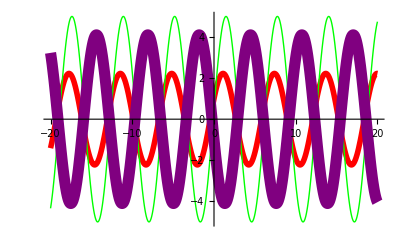

```mathematica
Sol= DSolve[y''[x]+y[x]==0,y[x],x]
Sol1= Evaluate[y[x]/.Sol[[1]]/.{C[1]->1,C[2]->2}]
Sol2=y[x]/.Sol[[1]]/.{C[1]->1/2,C[2]->5}
Sol3= y[x]/.Sol[[1]]/.{C[1]->-1,C[2]->-4}
Plot[{Sol1,Sol2,Sol3},{x,-20,20},PlotStyle->{{Red,Thickness[0.01]},{Green,Thick},{Purple,Thickness[0.02]}}]
```

{{y[x]→ⅇ^(-3 x) C[1]+ⅇ^(2 x) C[2]}}

2.5 ⅇ^(2 x)

ⅇ^(-3 x)+5 ⅇ^(2 x)

-1/2 ⅇ^(-3 x)+5 ⅇ^(2 x)

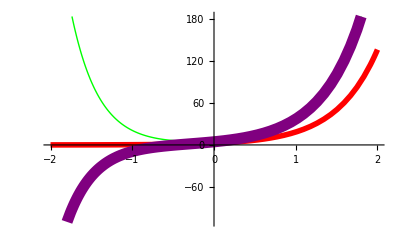

```mathematica
Sol= DSolve[y''[x]+y'[x]-6y[x]==0,y[x],x]
Sol1= Evaluate[y[x]/.Sol[[1]]/.{C[1]->0,C[2]->2.5}]
Sol2=y[x]/.Sol[[1]]/.{C[1]->1,C[2]->5}
Sol3= y[x]/.Sol[[1]]/.{C[1]->-1/2,C[2]->5}
Plot[{Sol1,Sol2,Sol3},{x,-2,2},PlotStyle->{{Red,Thickness[0.01]},{Green,Thick},{Purple,Thickness[0.02]}}]
```

{{y[x]→ⅇ^(-3 x/2) C[1]+ⅇ^(-3 x/2) x C[2]}}

-ⅇ^(-3 x/2)+4 ⅇ^(-3 x/2) x

3 ⅇ^(-3 x/2)+6 ⅇ^(-3 x/2) x

10 ⅇ^(-3 x/2)+7 ⅇ^(-3 x/2) x

-1.5 ⅇ^(-3 x/2)-5 ⅇ^(-3 x/2) x

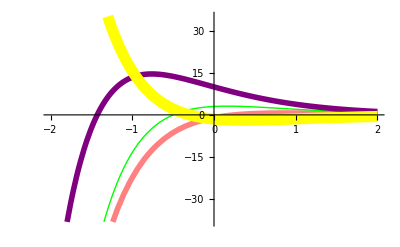

```mathematica
Sol= DSolve[4*y''[x]+12*y'[x]+9*y[x]==0,y[x],x]
Sol1= Evaluate[y[x]/.Sol[[1]]/.{C[1]->-1,C[2]->4}]
Sol2=y[x]/.Sol[[1]]/.{C[1]->3,C[2]->6}
Sol3= y[x]/.Sol[[1]]/.{C[1]->10,C[2]->7}
Sol4=y[x]/.Sol[[1]]/.{C[1]->-1.5,C[2]->-5}
Plot[{Sol1,Sol2,Sol3,Sol4},{x,-2,2},PlotStyle->{{Pink,Thickness[0.01]},{Green,Thick},{Purple,Thickness[0.01]},{Yellow,Thickness[0.02]}}]
```

{{y[x]→ⅇ^(3 x) C[2] Cos[2 x]+ⅇ^(3 x) C[1] Sin[2 x]}}

4 ⅇ^(3 x) Cos[2 x]-ⅇ^(3 x) Sin[2 x]

6 ⅇ^(3 x) Cos[2 x]+3 ⅇ^(3 x) Sin[2 x]

7 ⅇ^(3 x) Cos[2 x]-10 ⅇ^(3 x) Sin[2 x]

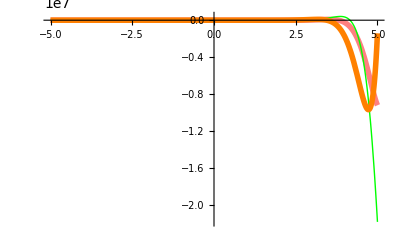

```mathematica
Sol= DSolve[y''[x]-6y'[x]+13y[x]==0,y[x],x]
Sol1= Evaluate[y[x]/.Sol[[1]]/.{C[1]->-1,C[2]->4}]
Sol2=y[x]/.Sol[[1]]/.{C[1]->3,C[2]->6}
Sol3= y[x]/.Sol[[1]]/.{C[1]->-10,C[2]->7}
Plot[{Sol1,Sol2,Sol3},{x,-5,5},PlotStyle->{{Pink,Thickness[0.01]},{Green,Thick},{Orange,Thickness[0.01]}},PlotRange->All]
```

{{y[x]→ⅇ^x C[1]+ⅇ^x x C[2]}}

0.5 ⅇ^x+3 ⅇ^x x

-3 ⅇ^x-2 ⅇ^x x

-ⅇ^x+7 ⅇ^x x

-6 ⅇ^x+ⅇ^x x

ⅇ^x/5+(2 ⅇ^x x)/3

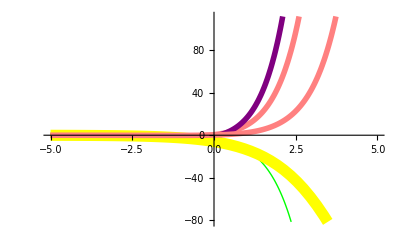

```mathematica
Sol= DSolve[y''[x]-2*y'[x]+y[x]==0,y[x],x]
Sol1= Evaluate[y[x]/.Sol[[1]]/.{C[1]->0.5,C[2]->3}]
Sol2=y[x]/.Sol[[1]]/.{C[1]->-3,C[2]->-2}
Sol3= y[x]/.Sol[[1]]/.{C[1]->-1,C[2]->7}
Sol4=y[x]/.Sol[[1]]/.{C[1]->-6,C[2]->1}
Sol5=y[x]/.Sol[[1]]/.{C[1]-> 1/5,C[2]-> 2/3}
Plot[{Sol1,Sol2,Sol3,Sol4,Sol5},{x,-5,5},PlotStyle->{{Pink,Thickness[0.01]},{Green,Thick},{Purple,Thickness[0.01]},{Yellow,Thickness[0.02]}}]
```

{{y[x]→ⅇ^x C[1]+ⅇ^(2 x) C[2]+ⅇ^(2 x) x C[3]}}

0.5 ⅇ^x+3 ⅇ^(2 x)+2/3 ⅇ^(2 x) x

-ⅇ^x/2+ⅇ^(2 x) x

-ⅇ^x-4 ⅇ^(2 x)+2 ⅇ^(2 x) x

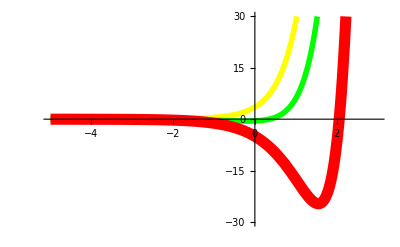

```mathematica
Sol= DSolve[y'''[x]-5*y''[x]+8y'[x]-4y[x]==0,y[x],x]
Sol1= Evaluate[y[x]/.Sol[[1]]/.{C[1]->0.5,C[2]->3,C[3]-> 2/3}]
Sol2=y[x]/.Sol[[1]]/.{C[1]->-1/2,C[2]->0,C[3]->1}
Sol3= y[x]/.Sol[[1]]/.{C[1]->-1,C[2]->-4,C[3]-> 2}
Plot[{Sol1,Sol2,Sol3},{x,-5 ,3},PlotRange-> {-30,30},PlotStyle->{{Yellow,Thickness[0.01]},{Green,Thickness[0.01]},{Red,Thickness[0.02]}}]
```

{{y[x]→ⅇ^(-7 x) C[1]+ⅇ^x C[2]+ⅇ^(3 x) C[3]}}

ⅇ^(-7 x)+2 ⅇ^(3 x)

-1/2 ⅇ^(-7 x)+ⅇ^(3 x)

-ⅇ^(-7 x)-4 ⅇ^x+2 ⅇ^(3 x)

-0.5 ⅇ^(-7 x)-2 ⅇ^x+ⅇ^(3 x)

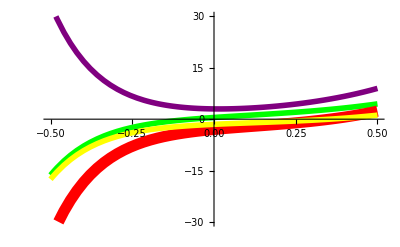

```mathematica
Sol= DSolve[y'''[x]+3*y''[x]-25y'[x]+21y[x]==0,y[x],x]
Sol1= Evaluate[y[x]/.Sol[[1]]/.{C[1]->1,C[2]->0,C[3]-> 2}]
Sol2=y[x]/.Sol[[1]]/.{C[1]->-1/2,C[2]->0,C[3]->1}
Sol3= y[x]/.Sol[[1]]/.{C[1]->-1,C[2]->-4,C[3]-> 2}
Sol4= y[x]/.Sol[[1]]/.{C[1]->-0.5,C[2]->-2,C[3]-> 1}
Plot[{Sol1,Sol2,Sol3,Sol4},{x,-0.5 ,0.5},PlotRange-> {-30,30},PlotStyle->{{Purple,Thickness[0.01]},{Green,Thickness[0.01]},{Red,Thickness[0.02]},{Yellow,Thickness[0.01]}}]
```

{{y[x]→ⅇ^(-4 x) C[1]+ⅇ^x C[2]+ⅇ^(7 x) C[3]}}

ⅇ^(-4 x)+2 ⅇ^(7 x)

-2 ⅇ^(-4 x)+10 ⅇ^x+3 ⅇ^(7 x)

-ⅇ^(-4 x)-4 ⅇ^x+20 ⅇ^(7 x)

-0.5 ⅇ^(-4 x)-2 ⅇ^x+ⅇ^(7 x)

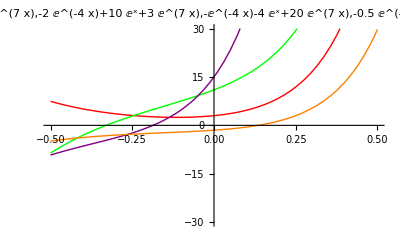

```mathematica
Sol= DSolve[y'''[x]-4*y''[x]-25y'[x]+28y[x]==0,y[x],x]
Sol1= Evaluate[y[x]/.Sol[[1]]/.{C[1]->1,C[2]->0,C[3]-> 2}]
Sol2=y[x]/.Sol[[1]]/.{C[1]->-2,C[2]->10,C[3]->3}
Sol3= y[x]/.Sol[[1]]/.{C[1]->-1,C[2]->-4,C[3]-> 20}
Sol4= y[x]/.Sol[[1]]/.{C[1]->-0.5,C[2]->-2,C[3]-> 1}
Plot[{Sol1,Sol2,Sol3,Sol4},{x,-0.5,0.5},PlotRange-> {-30,30},PlotStyle->{Red,Green,Purple,Orange},PlotLabel->{Sol1,Sol2,Sol3,Sol4}]
```

```mathematica
Sol= DSolve[y'''[x]-13*y''[x]+19y'[x]+33y[x]==Cos[2*x],y[x],x]
Sol1= Evaluate[y[x]/.Sol[[1]]/.{C[1]->1,C[2]->0,C[3]-> 2}]
Sol2=y[x]/.Sol[[1]]/.{C[1]->10,C[2]->3,C[3]->6}
Sol3= y[x]/.Sol[[1]]/.{C[1]->-1,C[2]->-7,C[3]-> 0.7}
Sol4= y[x]/.Sol[[1]]/.{C[1]->-10.5,C[2]->2,C[3]-> 1}
Plot[{Sol1,Sol2,Sol3,Sol4},{x,4 ,6},PlotStyle->{{Purple,Thickness[0.01]},{Green,Thickness[0.01]},{Red,Thickness[0.02]},{Yellow,Thickness[0.01]}}]
```

{{y[x]→ⅇ^-x C[1]+ⅇ^(3 x) C[2]+ⅇ^(11 x) C[3]+(17 Cos[2 x]+6 Sin[2 x])/1625}}

ⅇ^-x+2 ⅇ^(11 x)+(17 Cos[2 x]+6 Sin[2 x])/1625

10 ⅇ^-x+3 ⅇ^(3 x)+6 ⅇ^(11 x)+(17 Cos[2 x]+6 Sin[2 x])/1625

-ⅇ^-x-7 ⅇ^(3 x)+0.7 ⅇ^(11 x)+(17 Cos[2 x]+6 Sin[2 x])/1625

-10.5 ⅇ^-x+2 ⅇ^(3 x)+ⅇ^(11 x)+(17 Cos[2 x]+6 Sin[2 x])/1625

-Graphics-

{{y[x]→ⅇ^(2^(1/3) x) C[3]+ⅇ^(-x/2^(2/3)) C[1] Cos[(√3 x)/2^(2/3)]+ⅇ^(-x/2^(2/3)) C[2] Sin[(√3 x)/2^(2/3)]}}

2 ⅇ^(2^(1/3) x)+ⅇ^(-x/2^(2/3)) Cos[(√3 x)/2^(2/3)]

6 ⅇ^(2^(1/3) x)+10 ⅇ^(-x/2^(2/3)) Cos[(√3 x)/2^(2/3)]+3 ⅇ^(-x/2^(2/3)) Sin[(√3 x)/2^(2/3)]

0.7 ⅇ^(2^(1/3) x)-ⅇ^(-x/2^(2/3)) Cos[(√3 x)/2^(2/3)]-7 ⅇ^(-x/2^(2/3)) Sin[(√3 x)/2^(2/3)]

ⅇ^(2^(1/3) x)-10.5 ⅇ^(-x/2^(2/3)) Cos[(√3 x)/2^(2/3)]+2 ⅇ^(-x/2^(2/3)) Sin[(√3 x)/2^(2/3)]

10 ⅇ^(2^(1/3) x)+15 ⅇ^(-x/2^(2/3)) Cos[(√3 x)/2^(2/3)]-6 ⅇ^(-x/2^(2/3)) Sin[(√3 x)/2^(2/3)]

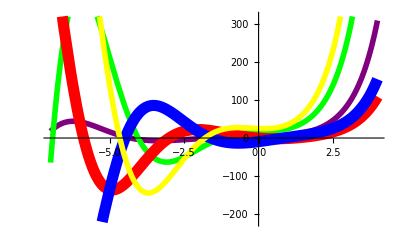

```mathematica
Sol= DSolve[y'''[x]-2y[x]==0,y[x],x]
Sol1= Evaluate[y[x]/.Sol[[1]]/.{C[1]->1,C[2]->0,C[3]-> 2}]
Sol2=y[x]/.Sol[[1]]/.{C[1]->10,C[2]->3,C[3]->6}
Sol3= y[x]/.Sol[[1]]/.{C[1]->-1,C[2]->-7,C[3]->0.7}
Sol4= y[x]/.Sol[[1]]/.{C[1]->-10.5,C[2]->2,C[3]-> 1}
Sol5= y[x]/.Sol[[1]]/.{C[1]->15,C[2]->-6,C[3]-> 10}
Plot[{Sol1,Sol2,Sol3,Sol4,Sol5},{x,-7 ,4},PlotStyle->{{Purple,Thickness[0.01]},{Green,Thickness[0.01]},{Red,Thickness[0.02]},{Blue,Thickness[0.02]},{Yellow,Thickness[0.01]}}]
```